```mathematica
wavelengthCylindricalInterferometer=658.0   *10^-9 (*Multiply by interferometer wavelength,units:data *);
```

## initial Scratch

#### convert to zygo format

```mathematica
convertNASAcylindricalDataToZygoXYZ[
(* fileName_ *)"E:\\ScanDataFiles\\NASAcylindricalWavefrontInterferometer\\20231108 - HighRi - Phase II - Sample 1\\20231108-1130-HighRi-P2-Sample1-ROC34mm-Mask20mm-12.h5",
(* maskXstart_ *)maskXstartSample1 ,
(* maskXend_ *)maskXendSample1 ,
(* maskYstart_ *)maskYstartSample1,
(* maskYend_ *)maskYendSample1,
(* pixelSizeInNanometers_ *)31250
]
```

E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\20231108 - HighRi - Phase II - Sample 1\20231108-1130-HighRi-P2-Sample1-ROC34mm-Mask20mm-12.xyz

#### reading a file

```mathematica
aDatasetQQ=Import[ToString["E:\\ScanDataFiles\\NASAcylindricalWavefrontInterferometer\\20231108 - HighRi - Phase II - Sample 1\\20231108-1130-HighRi-P2-Sample1-ROC34mm-Mask20mm-12.h5"],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}];
```

```mathematica
dimensionsOfImageArrayData[
aDatasetQQ
]
```

{982,1003}

```mathematica
Image[
normalizeAmplitudeOf2Darray[
maskImageDataToPoints[
aDatasetQQ,
(* maskXstart_ *)400,
(* maskXend_ *)982,
(* maskYstart_ *)200,
(* maskYend_ *)900
]
]
]
```

-Graphics-

```mathematica
Image[
normalizeAmplitudeOf2Darray[
aDatasetQQ
]
]
```

-Graphics-

### sub - aperture (full)

```mathematica
maskXstartSample1 = 540;
maskXendSample1 = 980;
maskYstartSample1 = 525;
maskYendSample1= 730;

Image[
normalizeAmplitudeOf2Darray[
maskImageDataToPoints[
aDatasetQQ,
(* maskXstart_ *)maskXstartSample1 ,
(* maskXend_ *)maskXendSample1 ,
(* maskYstart_ *)maskYstartSample1,
(* maskYend_ *)maskYendSample1
]
]
]
```

-Graphics-

### sub - aperture (partial)

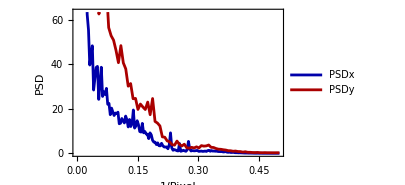
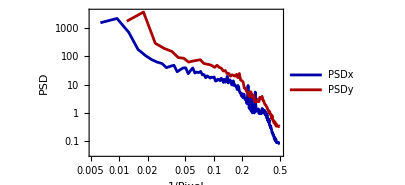
(RMS :   
86.8722
Peak to Valley : 
651.
{ Min ,  Max } :
{99.,750.}
{ numXcoords , numYcoords }  : 
{316,166}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
86.803
-Graphics-
-Graphics-)

```mathematica
quickLookAtImageData[
maskImageDataToPoints[
aDatasetQQ,
 maskXstart = maskXstartSample1 +40,
 maskXend =maskXendSample1 -85,
maskYstart = maskYstartSample1+20,
maskYend =maskYendSample1-20
]
]//MatrixForm
```

```mathematica
Image[
normalizeAmplitudeOf2Darray[
maskImageDataToPoints[
aDatasetQQ,
 maskXstart = maskXstartSample1 ,
 maskXend =maskXendSample1 ,
maskYstart = maskYstartSample1,
maskYend =maskYendSample1
]
]
]
```

-Graphics-

```mathematica
Image[
normalizeAmplitudeOf2Darray[
maskImageDataToPoints[
aDatasetQQ,
 maskXstart = maskXstartSample1 +10,
 maskXend =maskXendSample1-75 ,
maskYstart = maskYstartSample1+15,
maskYend =maskYendSample1-15
]
]
]
```

-Graphics-

### masking all the datasets to the same size

```mathematica
xStarts = Join[{maskXstartSample2process-45 ,maskXstartSample2process-45},Table[maskXstartSample2process, {nn,1,Length[sample2files]-2}]]
yStarts = Join[{maskYstartSample2process-5 ,maskYstartSample2process-5},Table[maskYstartSample2process, {nn,1,Length[sample2files]-2}]]
```

{645,645,690,690,690,690,690,690,690,690,690,690,690,690}

{505,505,510,510,510,510,510,510,510,510,510,510,510,510}

```mathematica
sample1regionsForProcessing = Table[
maskImageDataToPoints[
wavelengthCylindricalInterferometer*Import[ToString[sample1files[[nn]]],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}],
maskXstartSample1 +10,
maskXendSample1-75 ,
maskYstartSample1+15,
maskYendSample1-15
],
{nn,1,Length[sample1files]}
];
```

```mathematica
Table[
Image[
normalizeAmplitudeOf2Darray[
sample1regionsForProcessing[[nn]]
]
],
{nn, 1,Length[sample1files]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sample1QuickLook =Table[
quickLookAtImageData[
sample1regionsForProcessing[[nn]] 
],
{nn,1,Length[sample1files]}
];
```

```mathematica
sample1psdPlotsQuickLook = Table[
sample1QuickLook[[nn]][[-1]],
{nn,1,Length[sample1files]}
];
```

```mathematica
sample1psdPlotsQuickLook
```

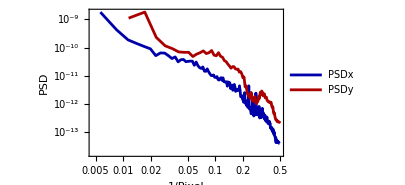
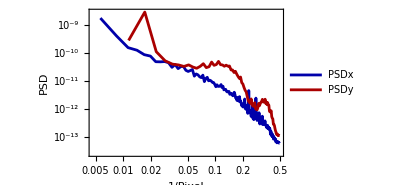
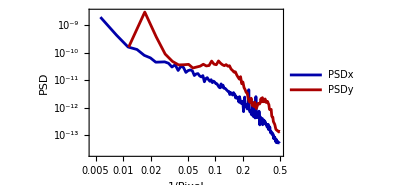
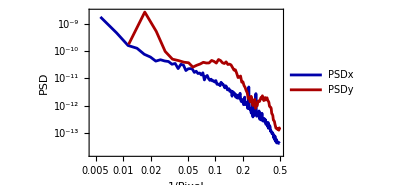
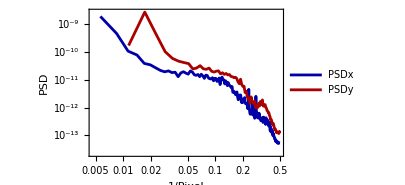
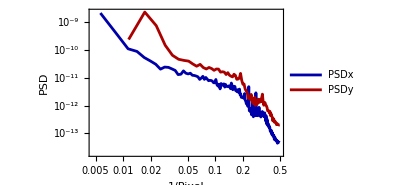
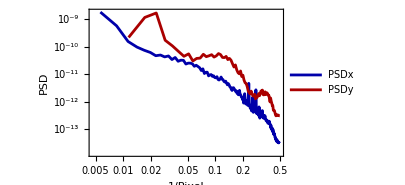
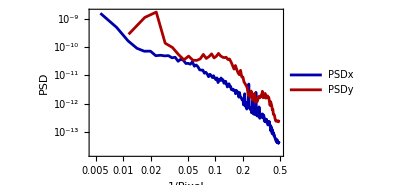

```mathematica
31.250*250
```

7812.5

## Inspection 20231108 - HighRi - Phase II - Sample 1

#### Defining coordinates of mask, and pointing to directory

```mathematica
maskXstart = maskXstartSample1 +40;
 maskXend =maskXendSample1 -85;
maskYstart = maskYstartSample1+20;
maskYend =maskYendSample1-20;
```

```mathematica
sample1files = FileNames["E:\\ScanDataFiles\\NASAcylindricalWavefrontInterferometer\\20231108 - HighRi - Phase II - Sample 1\\*.h5"
];
```

#### loading to memory

```mathematica
lookAtSubAp=Table[
quickLookAtImageData[
maskImageDataToPoints[
wavelengthCylindricalInterferometer*Import[ToString[fileName],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}],
maskXstart,
 maskXend ,
maskYstart,
maskYend 
]
]//MatrixForm,
{fileName,sample1files}];
```

#### summary

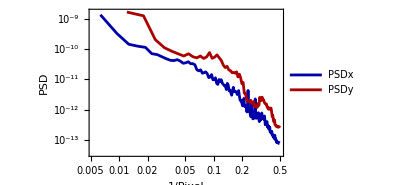
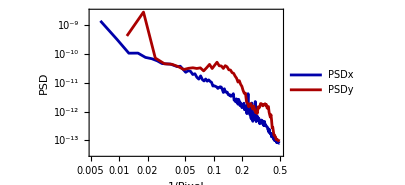
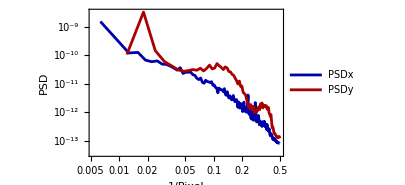
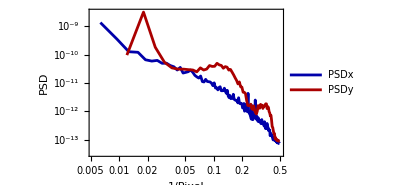
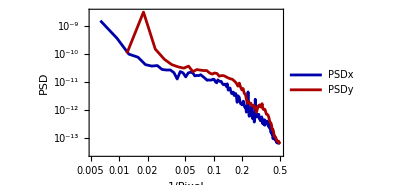
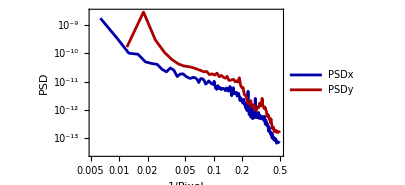
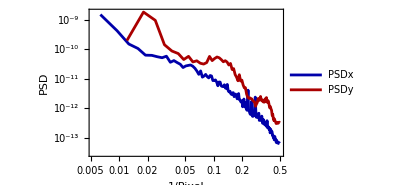
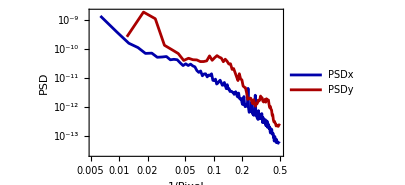
{(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-),(-Graphics-
-Graphics-)}

```mathematica
summaryOutputSubAp = Table[
{lookAtSubAp[[nn]][[-1]][[-5]],
lookAtSubAp[[nn]][[-1]][[-1]]}//MatrixForm,
{nn,1,Length[lookAtSubAp]}]
```

#### quickLookAtImageData

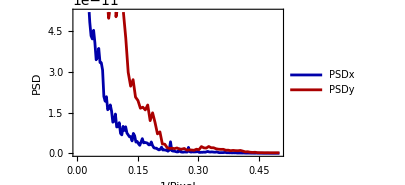
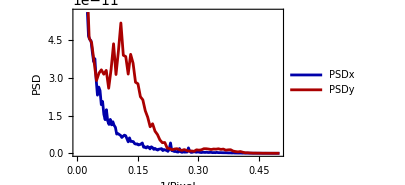
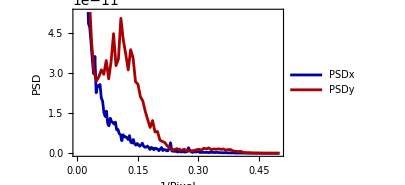
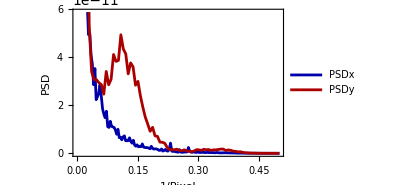
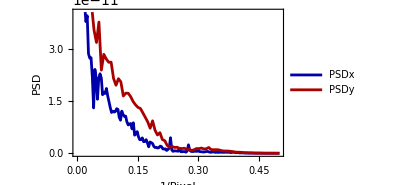
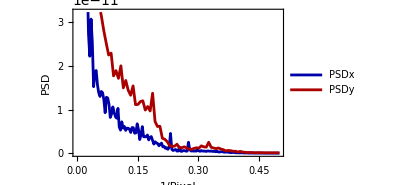
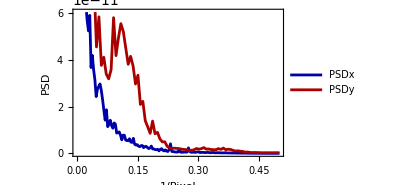
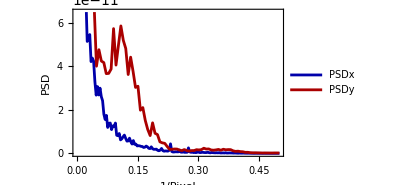
{(RMS :   
0.0000676555
Peak to Valley : 
0.000507976
{ Min ,  Max } :
{0.000060536,0.000568512}
{ numXcoords , numYcoords }  : 
{316,166}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000675922
-Graphics-
-Graphics-),(RMS :   
0.0000693306
Peak to Valley : 
0.000561274
{ Min ,  Max } :
{0.000051982,0.000613256}
{ numXcoords , numYcoords }  : 
{316,166}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000657669
-Graphics-
-Graphics-),(RMS :   
0.0000675482
Peak to Valley : 
0.000500738
{ Min ,  Max } :
{0.000061194,0.000561932}
{ numXcoords , numYcoords }  : 
{316,166}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000666085
-Graphics-
-Graphics-),(RMS :   
0.0000662882
Peak to Valley : 
0.00051982
{ Min ,  Max } :
{0.000060536,0.000580356}
{ numXcoords , numYcoords }  : 
{316,166}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000662769
-Graphics-
-Graphics-),(RMS :   
0.0000645306
Peak to Valley : 
0.000613914
{ Min ,  Max } :
{0.00005922,0.000673134}
{ numXcoords , numYcoords }  : 
{316,166}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.000064523
-Graphics-
-Graphics-),(RMS :   
0.0000654723
Peak to Valley : 
0.000433622
{ Min ,  Max } :
{0.000076986,0.000510608}
{ numXcoords , numYcoords }  : 
{316,166}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000641373
-Graphics-
-Graphics-),(RMS :   
0.0000661418
Peak to Valley : 
0.000538244
{ Min ,  Max } :
{0.000056588,0.000594832}
{ numXcoords , numYcoords }  : 
{316,166}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000658837
-Graphics-
-Graphics-),(RMS :   
0.0000668011
Peak to Valley : 
0.000542192
{ Min ,  Max } :
{0.000065142,0.000607334}
{ numXcoords , numYcoords }  : 
{316,166}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000665415
-Graphics-
-Graphics-),(RMS :   
0.0000657798
Peak to Valley : 
0.000534296
{ Min ,  Max } :
{0.00004277,0.000577066}
{ numXcoords , numYcoords }  : 
{316,166}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000655969
-Graphics-
-Graphics-),(RMS :   
0.0000598864
Peak to Valley : 
0.00047376
{ Min ,  Max } :
{0.00006251,0.00053627}
{ numXcoords , numYcoords }  : 
{316,166}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000596096
-Graphics-
-Graphics-),(RMS :   
0.0000601654
Peak to Valley : 
0.000474418
{ Min ,  Max } :
{0.000061194,0.000535612}
{ numXcoords , numYcoords }  : 
{316,166}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000600029
-Graphics-
-Graphics-),(RMS :   
0.0000571619
Peak to Valley : 
0.000428358
{ Min ,  Max } :
{0.000065142,0.0004935}
{ numXcoords , numYcoords }  : 
{316,166}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000571164
-Graphics-
-Graphics-)}

```mathematica
lookAtSubAp
```

```mathematica
lookAtSubAp[[1]]
```

(RMS :   
0.0000676555
Peak to Valley : 
0.000507976
{ Min ,  Max } :
{0.000060536,0.000568512}
{ numXcoords , numYcoords }  : 
{316,166}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000675922
-Graphics-
-Graphics-)

```mathematica
lookAtSubAp[[1]][[-1]][[-5]]
lookAtSubAp[[1]][[-1]][[-1]]
```

-Graphics-

-Graphics-